```mathematica
(*funkcja W(x)=(x+2)(x^2−3), W(x)=(x-2)(x^2−3),
W(x)=(x+2)(x^2+3),
W(x)=(x-2)(x^2+3) matura podstawowa grudzień 2022*)
```

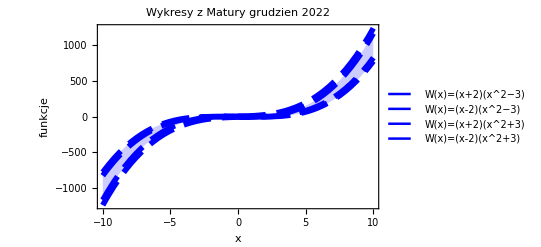

```mathematica
Plot[{(x+2)*(x^2-3),(x-2)*(x^2-3),(x+2)*(x^2+3),(x-2)*(x^2+3)},{x,-10,10},Frame->True,FrameLabel->{StyleForm["x ",FontSize->20,Red],StyleForm["funkcje",FontSize->10,Black]},PlotStyle->{{Thickness[0.01],Dashing[{0.05,0.02}],Blue}},PlotLegends->{"W(x)=(x+2)(x^2−3)","W(x)=(x-2)(x^2−3)","W(x)=(x+2)(x^2+3)","W(x)=(x-2)(x^2+3)"},BaseStyle->{FontFamily->Times,FontSize->16},ImageSize->Scaled[0.5],PlotLabel->StyleForm["Wykresy z Matury grudzien 2022",FontSize->14,Green],Filling->1->{2}]
```

```mathematica
(*obliczanie całek*)
(*x^4dx*)
```

```mathematica
Integrate[x^4,x]
```

x^5/5

```mathematica
(*dx/x+3*)
```

```mathematica
∫1/(x+3)ⅆx
```

Log[3+x]

```mathematica
(*sin[x]/Sqrt1+2*Cos[x])
```

```mathematica
Integrate[Sin[x]/Sqrt[1+2 Cos[x]],x]
```

-√(1+2 Cos[x])

```mathematica
(*x*Sin[x]cso[x]*)
```

```mathematica
Integrate[x*Sin[x]*Cos[x],{x,-Pi,Pi}]
```

-π/2

```mathematica
(*Cos[x/2]Cos[3x/2]*)
```

```mathematica
∫_0^Pi Cos[x/2]*Cos[3*x/2]ⅆx
```

0

```mathematica
(*(3z^3-5z^2+3)/(12z^2+4)^3*)
```

```mathematica
Integrate[(3z^3-5z^2+3)/(12z^2+4)^3,{z,5,0}]
```

-9875/4435968-(11 ArcTan[5 √3])/(768 √3)

```mathematica
(*granice*)
```

```mathematica
(*Lim[Sin[4x]/Sin[3x]]*)
```

```mathematica
Limit[Sin[4x]/Sin[3x],x->0]
```

4/3

```mathematica
(*Lim[Sqrt[3x]/x)
```

```mathematica
Limit[Sqrt[3x]/x,x->0]
```

∞

```mathematica
(*lim(1+(1/n))^n
```

```mathematica
Limit[(1+(1/n))^n,n->0]
```

```mathematica
1
```

1

```mathematica
(*limit[(3x^2-1)/(5x^2+2x)*)
```

```mathematica
Limit[(3x^2-1)/(5x^2+2x),x->0]
```

-∞

```mathematica
(*sin[x]/x*)
```

```mathematica
Limit[Sin[x]/x,x->Infinity]
```

0